```mathematica
?Arrow
```

Arrow[{pt_1,pt_2}] is a graphics primitive that represents an arrow from pt_1 to pt_2.
Arrow[{pt_1,pt_2},s] represents an arrow with its ends set back from pt_1 and pt_2 by a distance s. 
Arrow[{pt_1,pt_2},{s_1,s_2}] sets back by s_1 from pt_1 and s_2 from pt_2. 
Arrow[curve,…] represents an arrow following the specified curve.

```mathematica
?Line
```

Line[{p_1,p_2,…}] represents the line segments joining a sequence for points p_i.
Line[{{p_11,p_12,…},{p_21,…},…}] represents a collection of lines.

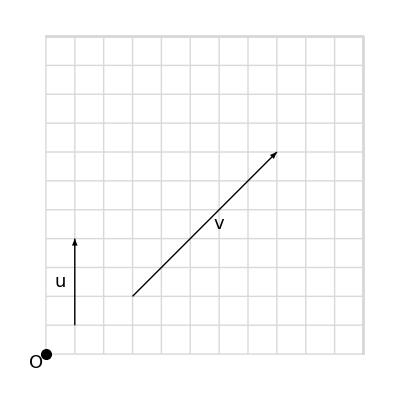

```mathematica
grid=Graphics[{LightGray,Table[Line[{{{i,j},{i+1,j}},{{i,j},{i,j+1}},{{0,11},{11,11}},{{11,0},{11,11}}}],{i,0,10},{j,0,10}]}];
vec1=Graphics[{Thick,Arrow[{{1,1},{1,4}}]}];
label1=Graphics[Text[Style["u",18],{0.5,2.5}]];
vec2=Graphics[{Thick,Arrow[{{3,2},{8,7}}]}];
label2=Graphics[Text[Style["v",18],{6,4.5}]];
origin=Graphics[{PointSize[0.02],Point[{0,0}]}];
labelO=Graphics[Text[Style["O",18], {-0.325,-0.325}]];

Show[grid,vec1,label1,vec2,label2,origin, labelO]
```

```mathematica
?Line
```

Line[{p_1,p_2,…}] represents the line segments joining a sequence for points p_i.
Line[{{p_11,p_12,…},{p_21,…},…}] represents a collection of lines.

```mathematica
?Point
```

Point[p] is a graphics and geometry primitive that represents a point at p. 
Point[{p_1,p_2,…}] represents a collection of points.